61

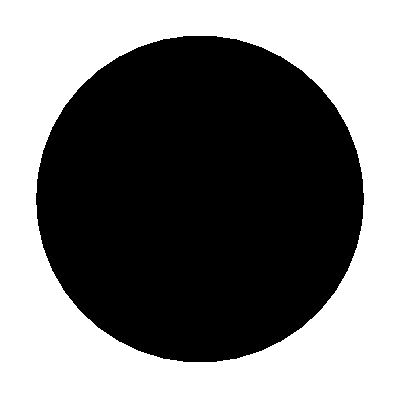

programming/Evolutionary/src/test/resources/physics/ball.obj

```mathematica
r=DiscretizeRegion[Disk[],MaxCellMeasure->0.1];
c=MeshCells[r,2];
in=MeshCoordinates[r];
Length[in]
Graphics[c/.i_Integer:> in[[i]]]
Export["programming/Evolutionary/src/test/resources/physics/ball.obj", r]
```

```mathematica
in
```

{{1.,0.},{0.988831,0.149042},{0.955573,0.294755},{0.900969,0.433884},{0.826239,0.56332},{0.733052,0.680173},{0.62349,0.781831},{0.5,0.866025},{0.365341,0.930874},{0.222521,0.974928},{0.0747301,0.997204},{-0.0747301,0.997204},{-0.222521,0.974928},{-0.365341,0.930874},{-0.5,0.866025},{-0.62349,0.781831},{-0.733052,0.680173},{-0.826239,0.56332},{-0.900969,0.433884},{-0.955573,0.294755},{-0.988831,0.149042},{-1.,5.66554×10^-16},{-0.988831,-0.149042},{-0.955573,-0.294755},{-0.900969,-0.433884},{-0.826239,-0.56332},{-0.733052,-0.680173},{-0.62349,-0.781831},{-0.5,-0.866025},{-0.365341,-0.930874},{-0.222521,-0.974928},{-0.0747301,-0.997204},{0.0747301,-0.997204},{0.222521,-0.974928},{0.365341,-0.930874},{0.5,-0.866025},{0.62349,-0.781831},{0.733052,-0.680173},{0.826239,-0.56332},{0.900969,-0.433884},{0.955573,-0.294755},{0.988831,-0.149042},{-0.396834,-0.316464},{-0.285924,0.419374},{-0.592116,0.0443729},{-0.674616,-0.264767},{-0.408245,-0.598786},{0.149609,-0.48502},{-0.213613,0.692516},{-0.566604,0.451851},{0.439568,0.253785},{-0.102777,-0.68188},{0.408245,-0.598786},{0.175629,0.569374},{0.49293,0.531252},{0.578889,-0.132128},{0.706543,0.161264},{0.163256,-0.0640732},{-0.210482,0.0176485},{-0.083895,-0.271981},{0.0372716,0.255232}}

-Graphics-